# Lab 6 William Keilsohn Section 32 April 17, 2014

1a: Consider the function f(x). For what x values is f(x) defined and then plot over that interval.

```mathematica
Quit[]
```

```mathematica
f[x_]=(x^2)*Sqrt[(2-x-x^2)]
```

x^2 √(2-x-x^2)

```mathematica
Solve[Sqrt[(2-x-x^2)]==0,x]
```

{{x→-2},{x→1}}

Therefore the function is defined on the interval [-2,1].

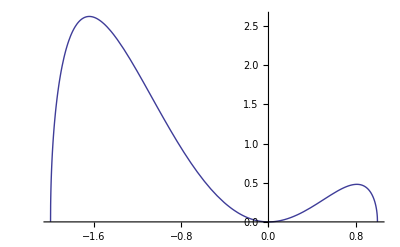

```mathematica
Plot[f[x],{x,-2,1}]
```

1b: Find all x values when f(x)=1 and use the graph to demonstrate how you found them.

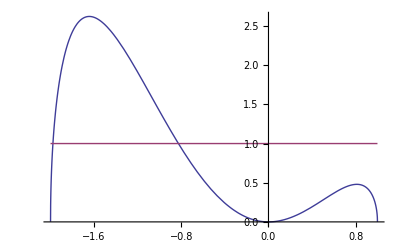

```mathematica
Plot[{f[x],1}, {x,-2.,1.}]
```

```mathematica
NSolve[f[x]==1,x,Reals]
```

{{x→-1.97807},{x→-0.826462}}

Therefore, since the horizantal line y=1, is intercepted by f(x) at x=-1.978, and x=-0.826, one can conclude that these are the x values for which f(x)=1.

2a:Find the length of the curve y=e^x on the interval [0,ln2] accurate to the nearist thousands.

```mathematica
g[x_]=Exp[x]
```

ⅇ^x

```mathematica
h[x_]=Sqrt[1+(g'[x])^2]
```

√(1+ⅇ^(2 x))

```mathematica
NIntegrate[h[x],{x,0,Log[2]}]
```

```mathematica
1.2220161770866356``4
```

1.222

Therefore, the length of the curve is 1.222 units.

```mathematica
?Log
```

Log[z] gives the natural logarithm of z (logarithm to base e). 
Log[b,z] gives the logarithm to base b.

2b: Find an exact expression of the length from 2a.

```mathematica
Integrate[h[x],{x,0,Log[2]}]
```

-√2+√5+ArcTanh[√2]-ArcTanh[√5]

3: Evaluate the sumation from n=1 to M of 1/n, for M values of 2,4,8,16,32,64,128,256,512,1024. Express answers to the thousands place. What do you notice about these numbers? Is this consistant with the divergence of the harmonic series?

```mathematica
Sum[1/n,{n,1.,2.}]
```

```mathematica
1.5``4
```

1.5

```mathematica
Sum[1/n,{n,1.,4.}]
```

```mathematica
2.083333333333333``4
```

2.083

```mathematica
Sum[1/n,{n,1.,8.}]
```

```mathematica
2.7178571428571425``4
```

2.718

```mathematica
Sum[1/n,{n,1.,16.}]
```

```mathematica
3.3807289932289937``4
```

3.381

```mathematica
Sum[1/n,{n,1.,32.}]
```

```mathematica
4.05849519543652``4
```

4.058

```mathematica
Sum[1/n,{n,1.,64.}]
```

```mathematica
4.7438909037057675``4
```

4.744

```mathematica
Sum[1/n,{n,1.,128.}]
```

```mathematica
5.433147092589174``4
```

5.433

```mathematica
Sum[1/n,{n,1.,256.}]
```

```mathematica
6.124344962817281``4
```

6.124

```mathematica
Sum[1/n,{n,1.,512.}]
```

```mathematica
6.81651653454972``4
```

6.817

```mathematica
Sum[1/n,{n,1.,1024.}]
```

```mathematica
7.509175672278132``4
```

7.509

One notices that as the values for M increase, the values of the sumation also increase. This would imply that as M->Infinity, so does the value of the sumation approach infinity. Therefore, the series diverges. This controdicts the limit test, but is consistant with a p-series where p=1, and with the harmonic series as was taught in class. The below work was done to check for coreectness.

```mathematica
Limit[(1/x),x->Infinity]
```

0

```mathematica
Sum[1/n,{n,1,Infinity}]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 1/n